```mathematica
Number of dimenstions

n = 4;

Standrad Deviation

sigma = 2;

alpha = 1/(2*sigma^2);

Number of  sweeps in Monte Carlo time

M = 5000;

eta = 12

LimitInt = 2
Eps = 1/5 (* MC epsilon *)(*SingleCoordinateValueProb[x_] :=*)(*InitialPath = RandomReal[{-LimitInt,LimitInt},n];*)

termalizacja = {}

cnt =0

etaacceptance = {};(* QM Harmonic Oscilator Action*)

ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};

Omega = 0.5 (* Harmonic oscilator omega*)

PathInit= RandomReal[{-LimitInt,LimitInt},n]
PathInit = {100,100,100,100}
```

```mathematica
ActionMatrix
```

dimenstions Number of

Deviation Standrad

Carlo in Monte Number of sweeps time

12

2

1/5

{}

0

0.5

{-1.2695,-0.822316,-1.81686,-0.102912}

{100,100,100,100}

```mathematica
ActionMatrix
```

{{10.05,-5,0,-5},{-5,10.05,-5,0},{0,-5,10.05,-5},{-5,0,-5,10.05}}

```mathematica
ActionXPrime = Exp[-PathNew.ActionMatrix]
```

ⅇ^(-PathNew.{{10.05,-5,0,-5},{-5,10.05,-5,0},{0,-5,10.05,-5},{-5,0,-5,10.05}})

```mathematica
PathNew = PathInit

PathOld = PathInit
```

{1000,1000,1000,1000}

{1000,1000,1000,1000}

```mathematica
eta
```

1.5

```mathematica
Do[
Print[PathOld];
	FindNewCoordinateProposition = (RandomInteger[n-1]+1);	
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];
Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;
ActionXPrime = Exp[-PathNew.ActionMatrix];
ActionX =  Exp[-PathOld.ActionMatrix];
If[ActionXPrime[[FindNewCoordinateProposition]]<ActionX[[FindNewCoordinateProposition]];,
cnt++;PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]];,
If[RandomReal[]<(ActionXPrime[[FindNewCoordinateProposition]]/ActionX[[FindNewCoordinateProposition]]),
	cnt++;
	PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]];
, ],
(**)];
		Print[PathOld];
,{n}	];

PathOld

PathNew
```

{1000,1000,1000,1000}

{1000,1000,1000,1000}

{1000,1000,1000,1000}

«5 more identical outputs»

{1000,1000,1000,1000}

{998.593,1000.29,998.992,1000.}

```mathematica
ActionXPrime[[FindNewCoordinateProposition]]

ActionX[[FindNewCoordinateProposition]]
```

17.6651

7.50298

```mathematica
V1.M1
```

```mathematica
FindNewCoordinateProposition = (RandomInteger[n-1]+1)		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
Part[PathNew,FindNewCoordinateProposition] =  Part[PathOld,FindNewCoordinateProposition] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix		
ActionX =  PathOld.ActionMatrix		
If[ActionXPrime[[FindNewCoordinateProposition]]<ActionX[[FindNewCoordinateProposition]],			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;			If[RandomReal[]<(ActionXPrime[[FindNewCoordinateProposition]]/ActionX[[FindNewCoordinateProposition]]),			
cnt++;			
Part[PathOld,FindNewCoordinateProposition] =Part[PathNew,FindNewCoordinateProposition] ;			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			],		]
```

4

{-29.505,4.00276,-5.49236,31.107}

{-24.0215,4.00276,-0.00879866,20.085}

```mathematica
eta=10
```

10

```mathematica
PathNew = PathInit
PathOld = PathInit
Do[
Do[	
(* update n times old path
Print[PathOld]; *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)		
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,	
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];(* Print[PathOld];*)		(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	]
,{M}]
```

{100,100,100,100}

{100,100,100,100}

```mathematica
PathOld
```

{0.132035,0.112477,-0.00177338,-0.00731127}

```mathematica
Ustalenie eta dla konkretej wartosci sweepow
```

```mathematica
termalizacja = {}
Do[
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M}];
AppendTo[termalizacja,{eta,cnt/(n*M)}];,
{eta,Range[0,12,0.1]}]
```

{}

```mathematica
{cnt/(n*M),eta}
```

{151/200,1.5}

```mathematica
cnt
```

148

```mathematica
n*M
```

200

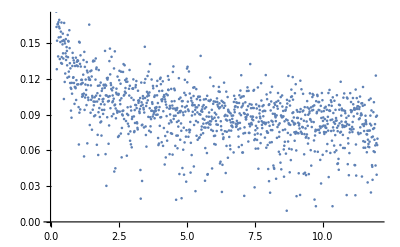

```mathematica
M = 50000;
ListPlot[termalizacja]
```

```mathematica
M = 5000;
ListPlot[termalizacja]
```

-Graphics-

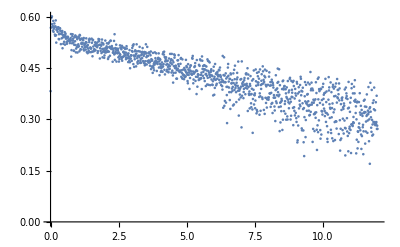

```mathematica
M = 500;
ListPlot[termalizacja]
```

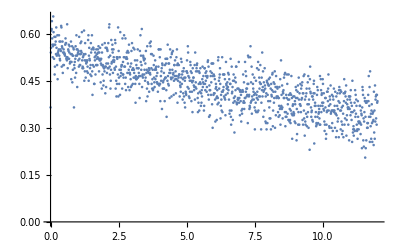

```mathematica
M = 50;
ListPlot[termalizacja]
```

```mathematica
termalizacja = {}
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
AppendTo[termalizacja,{cnt1,PathOld[[1]]}];
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M}];
```

{}

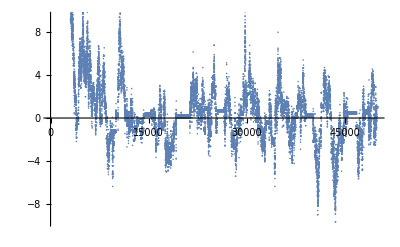

```mathematica
M = 50000;
ListPlot[termalizacja]
```

10

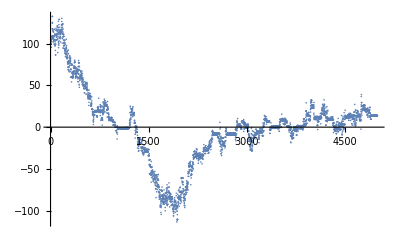

```mathematica
eta=10
M = 5000;
ListPlot[termalizacja]
```

5

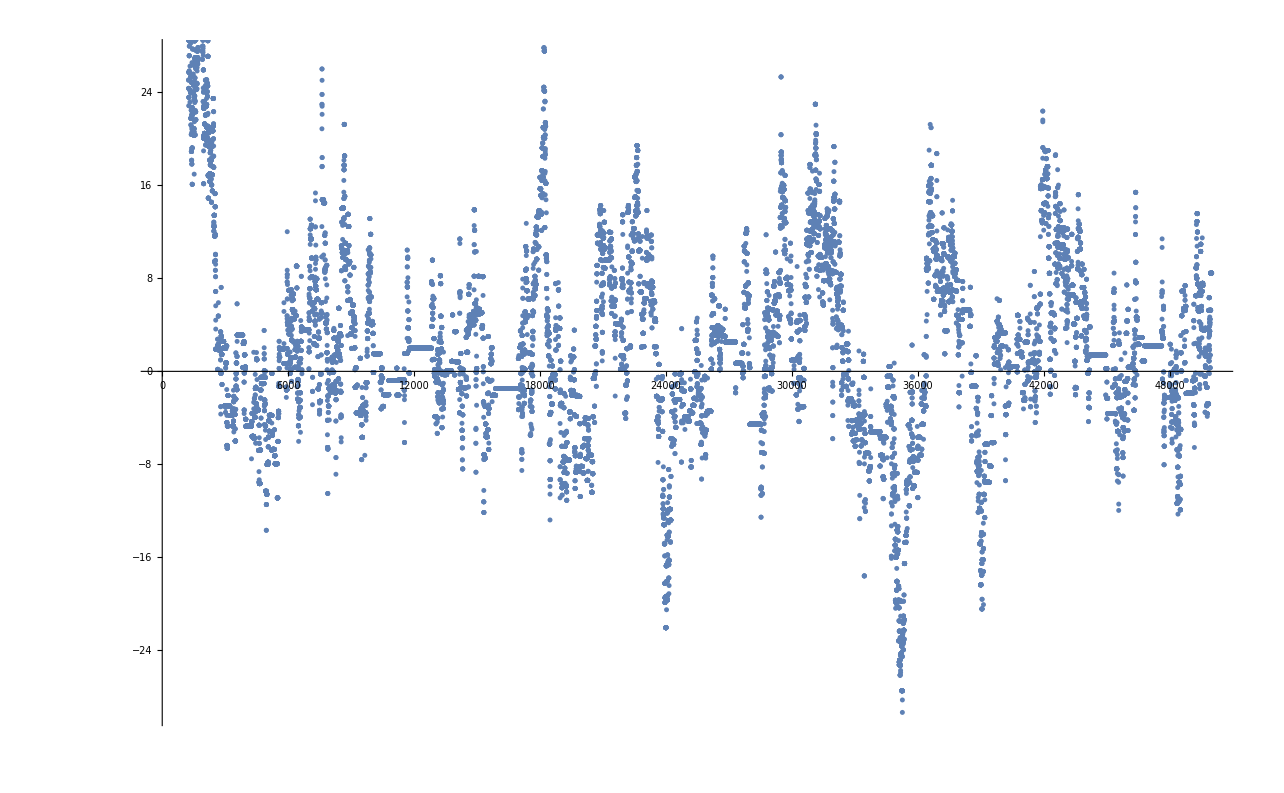

```mathematica
eta=5
M = 50000;
ListPlot[termalizacja]
```

```mathematica
termalizacja
```

{{1,100},{2,105.209},{3,100.623},{4,100.269},{5,100.269},{6,100.623},{7,106.734},{8,104.163},{9,99.384},{10,99.7827},{11,107.741},{12,103.052},{13,103.052},{14,95.7092},4972,{4987,14.2644},{4988,13.7097},{4989,13.9914},{4990,13.7097},{4991,13.7097},{4992,13.1823},{4993,14.2644},{4994,13.7097},{4995,13.9914},{4996,13.7097},{4997,13.7097},{4998,14.2644},{4999,13.1823},{5000,13.9914}}
 |  |  |  |

```mathematica
SREDNIE Eeta 5 M 50000
```

```mathematica
srednia = {}
eta=6
M = 50000;
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
AppendTo[srednia,{cnt1,PathOld[[1]],PathOld[[2]],PathOld[[3]],PathOld[[4]]}];
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M,4000,50000}];
```

{}

5

```mathematica
Srednia 1
```

```mathematica
Total[srednia[[1;All,2]]]/srednia[[46001,1]]
```

5.49251

```mathematica
Srednia 2
```

```mathematica
Total[srednia[[1;All,3]]]/srednia[[46001,1]]
```

5.54882

```mathematica
Srednia 3
```

```mathematica
Total[srednia[[1;All,4]]]/srednia[[46001,1]]
```

5.5477

```mathematica
Srednia 4
```

```mathematica
Total[srednia[[1;All,5]]]/srednia[[46001,1]]
```

5.4705

```mathematica
SREDNIE Eeta 6 M 500000
```

```mathematica
srednia = {}
eta=6
M = 500000;
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
AppendTo[srednia,{cnt1,PathOld[[1]],PathOld[[2]],PathOld[[3]],PathOld[[4]]}];
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M,4000,500000}];
```

{}

6

$Aborted

```mathematica
Srednia 1
```

Srednia

```mathematica
Total[srednia[[1;All,2]]]/srednia[[496001,1]]
```

5.01161

```mathematica
Srednia 2
```

2 Srednia

```mathematica
Total[srednia[[1;All,3]]]/srednia[[496001,1]]
```

5.08097

```mathematica
Srednia 3
```

3 Srednia

```mathematica
Total[srednia[[1;All,4]]]/srednia[[496001,1]]
```

5.10851

```mathematica
Srednia 4
```

4 Srednia

```mathematica
Total[srednia[[1;All,5]]]/srednia[[496001,1]]
```

5.00553

```mathematica
SREDNIE Eeta 6 M 10000 Eps 1
```

```mathematica
termalizacja1 = {}
termalizacja2 = {}
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
AppendTo[termalizacja1,{cnt1,PathOld[[1]],PathOld[[2]],PathOld[[3]],PathOld[[4]]}];
AppendTo[termalizacja2,{cnt1,PathOld[[1]]^2,PathOld[[2]]^2,PathOld[[3]]^2,PathOld[[4]]^2}];
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M}];
```

{}

{}

```mathematica
drMoment={}
srednia = {}
PathNew = PathInit;
PathOld = PathInit;
Trajectories ={};cnt= 0;
cnt1 = 0;
Do[	(* generate sweep *)	
Do[	(* update n times old path *)		
FindNewCoordinateProposition = (RandomInteger[n-1]+1);		
r = RandomReal[{0+$MachineEpsilon,1-$MachineEpsilon}];		
PathNew[[FindNewCoordinateProposition]] =  PathOld[[FindNewCoordinateProposition]] + (2*r-1)*eta;		
ActionXPrime = PathNew.ActionMatrix.PathNew;		
ActionX =  PathOld.ActionMatrix.PathOld;(*Print[ActionXPrime];Print[ActionX];*)			
If[ActionXPrime<ActionX,			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,		
If[RandomReal[]<(Exp[-ActionXPrime/ActionX]),			
cnt++;			
PathOld[[FindNewCoordinateProposition]] =PathNew[[FindNewCoordinateProposition]] ;,			(*Odrzucamy - przechodzimy do poczatku tego przejscia petli - continue ? lub wracamy do poczatkowego x *) 			(*Part[PathOld,FindNewCoordinateProposition] = Part[InitialPath,FindNewCoordinateProposition];			AppendTo[Trajectories,Part[PathOld,FindNewCoordinateProposition]] *)			
],		
];	
(*	Print[Part[PathOld,FindNewCoordinateProposition]];			Print[FindNewCoordinateProposition];*)		
,{n}	
];cnt1++;
AppendTo[srednia,{cnt1,PathOld[[1]],PathOld[[2]],PathOld[[3]],PathOld[[4]]}];
AppendTo[drMoment,{cnt1,PathOld[[1]]^2,PathOld[[2]]^2,PathOld[[3]]^2,PathOld[[4]]^2}];
(*If[cnt1==M,AppendTo[etaacceptance,{eta,cnt/M}];(*Print[eta,cnt/M]*),];*)
,{M,Start,10000}];
```

{}

{}

```mathematica
Epsilon 0.2
```

```mathematica
Akceptancja Eta
```

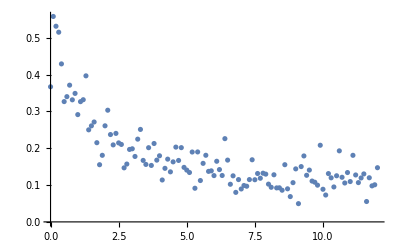

```mathematica
ListPlot[termalizacja]
```

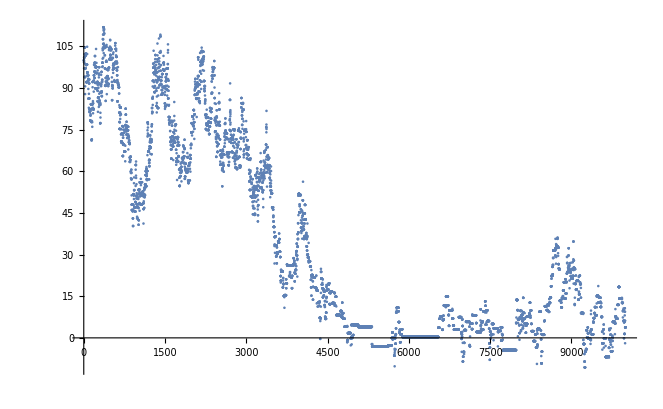

```mathematica
ListPlot[Transpose[{termalizacja1[[1;;All,1]],termalizacja1[[1;;All,3]]}]]
```

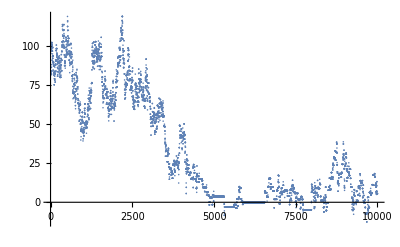

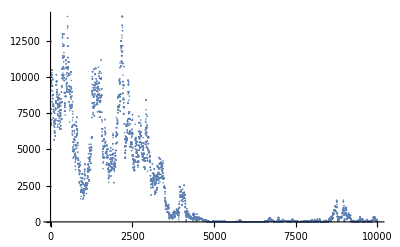

```mathematica
ListPlot[Transpose[{termalizacja1[[1;;All,1]],termalizacja1[[1;;All,2]]}]]
ListPlot[Transpose[{termalizacja2[[1;;All,1]],termalizacja2[[1;;All,2]]}]]
```

```mathematica
eta=7;
Eps = 0.2;
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Start = 5000;
Length[termalizacja1[[Start;;All,2]]]
M-Start
```

5001

5000

```mathematica
Srednia 1
```

```mathematica
termalizacja1[[Start]]
```

{2000,-4.37765,-5.28241,-4.69197,-4.31564}

```mathematica
Total[termalizacja1[[Start;;All,2]]]/(M-Start+1)
Total[termalizacja2[[Start;;All,2]]]/(M-Start+1)
```

5.31718

95.5705

```mathematica
Srednia 2
```

```mathematica
Total[termalizacja1[[Start;;All,3]]]/(M-Start+1)
Total[termalizacja2[[Start;;All,3]]]/(M-Start+1)
```

5.19649

93.0973

```mathematica
Srednia 3
```

```mathematica
Total[termalizacja1[[Start;;All,4]]]/(M-Start+1)
Total[termalizacja2[[Start;;All,4]]]/(M-Start+1)
```

5.33264

101.108

```mathematica
Srednia 4
```

```mathematica
Total[termalizacja1[[Start;;All,5]]]/(M-Start+1)
Total[termalizacja2[[Start;;All,5]]]/(M-Start+1)
```

5.28133

101.307

```mathematica
Epsilon 0.5
```

```mathematica
Akceptancja Eta
```

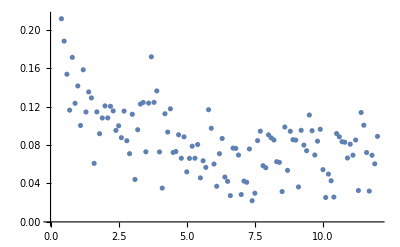

```mathematica
ListPlot[termalizacja]
```

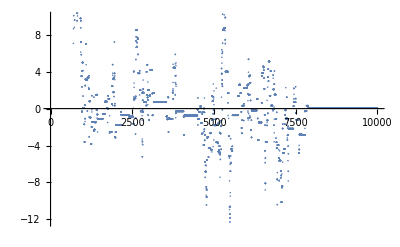

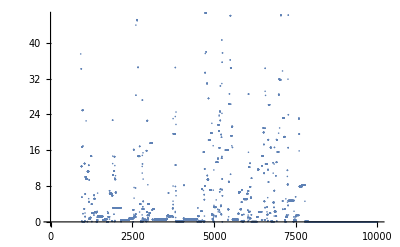

```mathematica
ListPlot[Transpose[{termalizacja1[[1;;All,1]],termalizacja1[[1;;All,3]]}]]
ListPlot[Transpose[{termalizacja2[[1;;All,1]],termalizacja2[[1;;All,3]]}]]
```

```mathematica
eta=4;
Eps = 0.5;
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Start=1000;
```

```mathematica
Srednia 1
```

```mathematica
Total[termalizacja1[[Start;;All,2]]]/(M-Start)
Total[termalizacja2[[Start;;All,2]]]/(M-Start)
```

-0.154726

6.04595

```mathematica
Srednia 2
```

```mathematica
Total[termalizacja1[[Start;;All,3]]]/(M-Start)
Total[termalizacja2[[Start;;All,3]]]/(M-Start)
```

-0.265806

6.2503

```mathematica
Srednia 3
```

```mathematica
Total[termalizacja1[[Start;;All,4]]]/(M-Start)
Total[termalizacja2[[Start;;All,4]]]/(M-Start)
```

-0.338482

5.78489

```mathematica
Srednia 4
```

```mathematica
Total[termalizacja1[[Start;;All,5]]]/(M-Start)
Total[termalizacja2[[Start;;All,5]]]/(M-Start)
```

-0.22244

5.7092

```mathematica
Epsilon 0.8
```

```mathematica
Akceptancja Eta
```

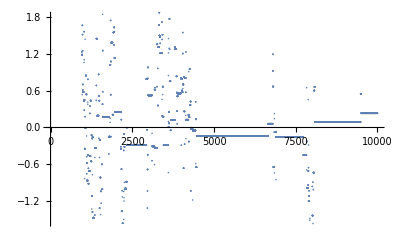

```mathematica
ListPlot[Transpose[{termalizacja1[[1;;All,1]],termalizacja1[[1;;All,3]]}]]
```

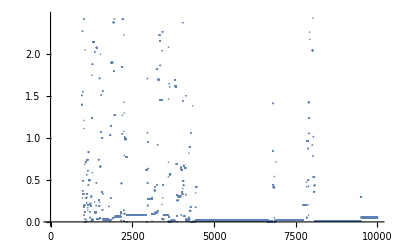

```mathematica
ListPlot[Transpose[{termalizacja2[[1;;All,1]],termalizacja2[[1;;All,3]]}]]
```

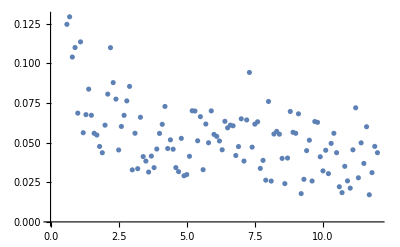

```mathematica
ListPlot[termalizacja]
```

```mathematica
eta=1.5;
Eps = 0.8;
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Start = 2000;
```

```mathematica
Srednia 1
```

```mathematica
Total[termalizacja1[[Start;;All,2]]]/(M-Start)
Total[termalizacja2[[Start;;All,2]]]/(M-Start)
```

0.0362208

0.184493

```mathematica
Srednia 2
```

```mathematica
Total[termalizacja1[[Start;;All,3]]]/(M-Start)
Total[termalizacja2[[Start;;All,3]]]/(M-Start)
```

0.0369272

0.217623

```mathematica
Srednia 3
```

```mathematica
Total[termalizacja1[[Start;;All,4]]]/(M-Start)
Total[termalizacja2[[Start;;All,4]]]/(M-Start)
```

-0.00552317

0.221411

```mathematica
Srednia 4
```

```mathematica
Total[termalizacja1[[Start;;All,5]]]/(M-Start)
Total[termalizacja2[[Start;;All,5]]]/(M-Start)
```

-0.000509827

0.216018

```mathematica
Epsilon 1
```

```mathematica
Akceptancja Eta
```

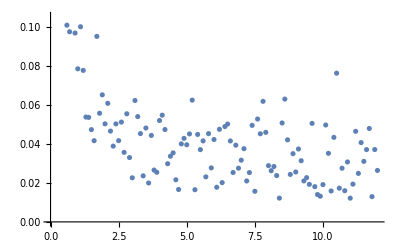

```mathematica
ListPlot[termalizacja]
```

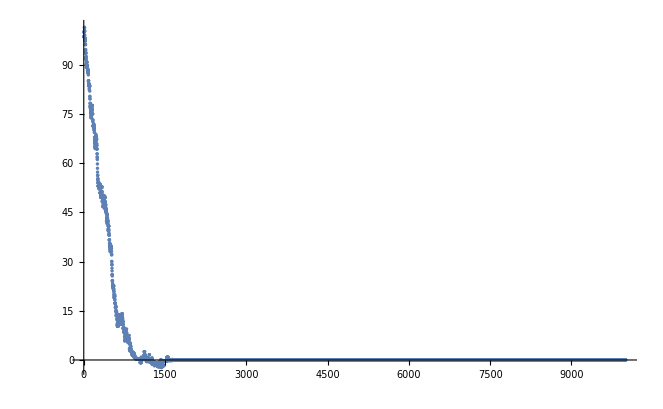

```mathematica
ListPlot[Transpose[{termalizacja1[[1;;All,1]],termalizacja1[[1;;All,3]]}]]
```

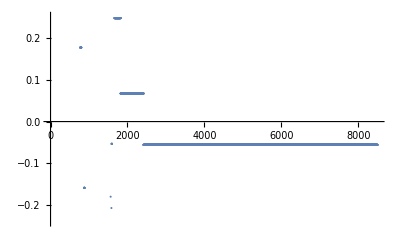

```mathematica
ListPlot[Transpose[{srednia[[1;;All,1]],srednia[[1;;All,3]]}]]
```

```mathematica
eta=1.5;
Eps = 1;
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Start = 1500;
```

```mathematica
Srednia 1
```

```mathematica
Total[termalizacja1[[Start;;All,2]]]/(M-Start)
```

0.0307993

```mathematica
Total[termalizacja2[[Start;;All,2]]]/(M-Start)
```

0.00400271

```mathematica
Srednia 2
```

```mathematica
Total[termalizacja1[[Start;;All,3]]]/(M-Start)
```

0.0536174

```mathematica
Total[termalizacja2[[Start;;All,3]]]/(M-Start)
```

0.00554373

```mathematica
Srednia 3
```

```mathematica
Total[termalizacja1[[Start;;All,4]]]/(M-Start)
```

0.0996036

```mathematica
Total[termalizacja2[[Start;;All,4]]]/(M-Start)
```

0.0127259

```mathematica
Srednia 4
```

```mathematica
Total[termalizacja1[[Start;;All,5]]]/(M-Start)
```

-0.023697

```mathematica
Total[termalizacja2[[Start;;All,5]]]/(M-Start)
```

0.00895439

```mathematica
eta=6
Eps = 0.8
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Srednia 1
```

6

0.8

Srednia

```mathematica
Total[srednia[[1;All,2]]]/srednia[[6001,1]]
```

3.41764

```mathematica
Srednia 2
```

2 Srednia

```mathematica
Total[srednia[[1;All,3]]]/srednia[[6001,1]]
```

3.26593

```mathematica
Srednia 3
```

3 Srednia

```mathematica
Total[srednia[[1;All,4]]]/srednia[[6001,1]]
```

3.26763

```mathematica
Srednia 4
```

4 Srednia

```mathematica
Total[srednia[[1;All,5]]]/srednia[[6001,1]]
```

3.32977

```mathematica
eta=6
Eps = 1
ActionMatrix = {{2/Eps+Eps*Omega^2,-1/Eps,0,-1/Eps},{-1/Eps,2/Eps+Eps*Omega^2,-1/Eps,0},{0,-1/Eps,2/Eps+Eps*Omega^2,-1/Eps},{-1/Eps,0,-1/Eps,2/Eps+Eps*Omega^2}};
M = 10000;
Srednia 1
```

Srednia

```mathematica
Total[srednia[[1;All,2]]]/srednia[[6001,1]]
```

2.69406

```mathematica
Srednia 2
```

2 Srednia

```mathematica
Total[srednia[[1;All,3]]]/srednia[[6001,1]]
```

2.7492

```mathematica
Srednia 3
```

3 Srednia

```mathematica
Total[srednia[[1;All,4]]]/srednia[[6001,1]]
```

2.89282

```mathematica
Srednia 4
```

4 Srednia

```mathematica
Total[srednia[[1;All,5]]]/srednia[[6001,1]]
```

2.51599